Лабораторная работа №4
                                                                                   Выполнила студентка ФПМИ БГУ
                                                                                          ПМ, 3к.,6гр.,Плещанкова Д.И.
                                                                                                                 23 декабря 2015
Задание 1.
Написать собственные функции нахождения решения системы дифференциальных уравнений методами Эйлера и Рунге-Кутта с точностью 10^-9  с шагом h=0.01 на отрезке [a, b].

метод Эйлера

NDSolve:

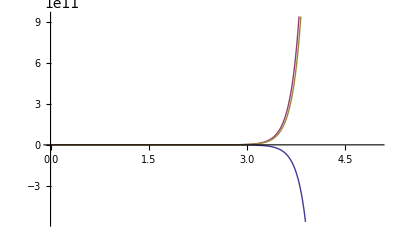

My Euler:

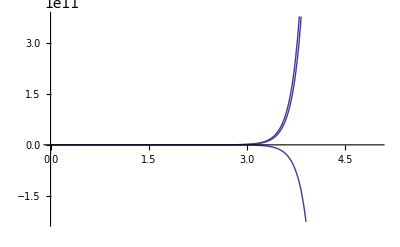

```mathematica
Eiler[system_,startDots_,a_,b_]:=Module[{n=Length[startDots],h=0.01,dots,newDots,points,result,res},
dots = startDots;
newDots=Table[,{i,n}];
points=Table[{},{i,n}];
For[i=1,i≤n,++i,
points⟦i⟧=Append[points⟦i⟧,{a,dots⟦i⟧}];
];
For[t=a+h,t≤b,t+=h,
For[i=1,i≤n,i++,
res =system⟦i⟧;
For[j=1,j≤n,j++,
res=res/.{Variables[res]⟦1⟧->dots⟦j⟧}];
newDots⟦i⟧=dots⟦i⟧+h*res;
points⟦i⟧=Append[points⟦i⟧,{t,newDots⟦i⟧}];
];
dots=newDots;
];
result=Table[Interpolation[points⟦i⟧],{i,1,n}];
Return[result];
];


Clear[t];
Print["NDSolve:"];
solution=NDSolve[{x'[t]==x[t]-y[t]-z[t],y'[t]==x[t]+5y[t]+3z[t],z'[t]==x[t]-z[t]+7y[t],x[0]==0,y[0]==1,z[0]==2},{x,y,z},{t,0,5}];
Plot[Evaluate[{x[t],y[t],z[t]}/.First[solution]],{t,0,5}]
Print["My Euler:"];
mySolution=Eiler[{x-y-z,x+5y+3z,x-z+7y},{0,1,2},0,5];
Plot[Table[mySolution⟦i⟧[t],{i,1,Length[mySolution]}],{t,0,5}]
```

метод Рунге-Кутта

Решение NDSolve:

-Graphics-

Решение методом Рунге-Кутта:

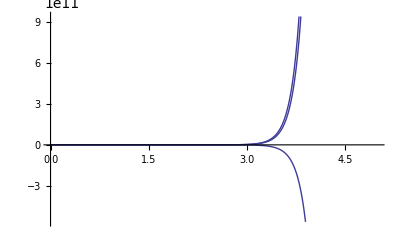

```mathematica
RungeKutta[system_,startDots_,a_,b_]:=Module[{n=Length[startDots],h=0.01,dots,newDots,points,result,k1,k2,k3,k4,res},
dots=startDots;
newDots=Table[,{i,n}];
points=Table[{},{i,n}];
k1=k2=k3=k4=Table[,{i,n}];
For[i=1,i≤n,++i,
points⟦i⟧=Append[points⟦i⟧,{a,dots⟦i⟧}];
];
For[t=a+h,t≤b,t+=h,
For[i=1,i≤n,i++,
res = system⟦i⟧;
For[j=1,j≤n,j++,
res=res/.{Variables[res]⟦1⟧->dots⟦j⟧};
];
k1⟦i⟧=N[res];
];
For[i=1,i≤n,i++,
res = system⟦i⟧;
For[j=1,j≤n,j++,
res=res/.{Variables[res]⟦1⟧->dots⟦j⟧+h/2 k1⟦j⟧};
];
k2⟦i⟧=N[res];
];
For[i=1,i≤n,i++,
res = system⟦i⟧;
For[j=1,j≤n,j++,
res=res/.{Variables[res]⟦1⟧->dots⟦j⟧+h/2 k2⟦j⟧};
];
k3⟦i⟧=N[res];
];
For[i=1,i≤n,i++,
res = system⟦i⟧;
For[j=1,j≤n,j++,
res=res/.{Variables[res]⟦1⟧->dots⟦j⟧+h*k3⟦j⟧};
];
k4⟦i⟧=N[res];
];
For[i=1,i≤n,i++,
newDots⟦i⟧=N[dots⟦i⟧+1/6 h(k1⟦i⟧+2k2⟦i⟧+2k3⟦i⟧+k4⟦i⟧)];
points⟦i⟧=Append[points⟦i⟧,{t,newDots⟦i⟧}];
];
dots=newDots;
];
result=Table[Interpolation[points⟦i⟧],{i,1,n}];
Return[result];
];

Clear[t];
Print["Решение NDSolve:"];
solution=NDSolve[{x'[t]==x[t]-y[t]-z[t],y'[t]==x[t]+5y[t]+3z[t],z'[t]==x[t]-z[t]+7y[t],x[0]==0,y[0]==1,z[0]==2},{x,y,z},{t,0,5}];
Plot[Evaluate[{x[t],y[t],z[t]}/.First[solution]],{t,0,5}]

Print["Решение методом Рунге-Кутта:"];
mySolution=RungeKutta[{x-y-z,x+5y+3z,x-z+7y},{0,1,2},0,5];
Plot[Table[mySolution⟦i⟧[t],{i,1,Length[mySolution]}],{t,0,5}]
```

Задание 2.
Метод Квадратур. Написать собственную функцию решения  интегрального уравнения методом квадратур с точностью 10^-9. Построить графики точного решения и решения, полученного методом квадратур.

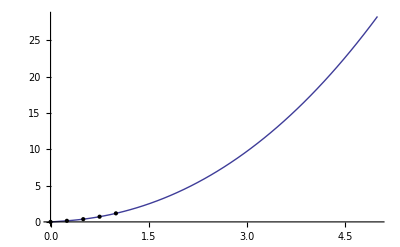

-Graphics-

```mathematica
QuadraticMetod[K_,lambda_,f_,a_,b_]:=Module[{h= 0.25,vectorX,vectorS,ind,summ = 0,expr,integralY,vectorExpr,solForSystem,k,points,solution},vectorX={};
vectorS={};ind = 0;
For[i=a,i≤b,i+=h,vectorX = Append[vectorX,i];vectorS= Append[vectorS,i];ind++]
For[j=1,j≤ind,j++,expr=(K/.s->vectorS[[j]]);If[j==1||j==ind,expr*=Subscript[y, j-1],expr*=4*Subscript[y, j-1]];summ+=expr];
integralY=h/3*summ;
vectorExpr = {};
For[k=a,k≤b,k+=h,vectorExpr = Append[vectorExpr,(lambda*(integralY/.t->k))+(f/.t->k)]];
solForSystem ={};
For[j=1,j≤ind,j++,solForSystem = Append[solForSystem,Subscript[y, j-1]==vectorExpr[[j]]]];
solution = N[Solve[solForSystem]]/.Rule->List;
points = {};

For[j=1;k = a,j≤ind,j++;k+=h,points = Append[points,{k,Part[Part[Part[solution,1],j],2]}]];Return[points]]
ClearAll[s,t];
lambda = 1/2;
K=√t*s;
f = t^2;
h= 0.25;
a = 0;
b = 1;
function = QuadraticMetod[K,lambda,f,a,b];
fun = Interpolation[function];
Plot[fun[x], {x,0,5}, Epilog->Map[Point, function]]
```

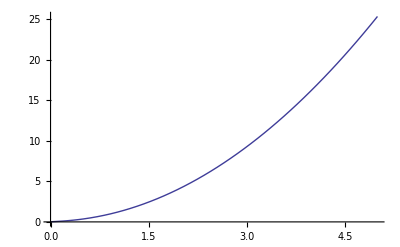

```mathematica
Plot[x^2+(5 √x)/32, {x,0,5}]
```